# Region from Mask

## archived code

```mathematica
(* Clear@findSym;
findSym[mask_,option_:False]:=Block[{imd,nx,ny,points,weights,mass,centerOfMass,pointsCom,diag,inertia,v1,v2},
imd=Transpose@ImageData[mask];(* here we transpose the image data *)
{nx,ny}=Dimensions[imd];(* dimensions of the image *)
points=Tuples[{Range[nx],Reverse@Range[ny]}]; (* x-y coordinates on the image *)
weights=Flatten[imd]; (* vector of imagedata *)

centerOfMass=ImageMeasurements[mask,"IntensityCentroid"];(* here we calculate the x-y coordinate of the center of mass *)

pointsCom=(Subtract[#,centerOfMass]&/@points) weights; (* we subtract from each point the center of mass. This gives us a vector of n number of points the {x,y} coordinates of which are displacements from the centroids. We multiply this resulting matrix with the intensity vector. This gives us a vector consisting of two coordinates which are x y displacments from centroid * intensity for each point in the grid *)

diag=Total[(#.#)&/@pointsCom]; (* sum of the {x,y}.{x,y} from above. gives a single values *)
inertia=Table[KroneckerDelta[i,j] diag-Total[(#[[i]] #[[j]])&/@pointsCom],{i,2},{j,2}]; (* inertia *)

{v1,v2}=Eigenvectors[inertia]; (* extracting eigenvectors from inertia *)
(* Print["center of Mass: ", centerOfMass,"\n","pt1 : ",v1 + centerOfMass,"\n","pt2 : ",v2 + centerOfMass]; *)

(* display *)
If[option,Print@Show[mask,Graphics[{{Thick,Dashed,XYZColor[0,0,1,0.6],InfiniteLine[{v2+centerOfMass,centerOfMass}]},{Thick,Dashed,XYZColor[1,0,0,0.6],InfiniteLine[{v1+centerOfMass,centerOfMass}]},{Darker@XYZColor[0,1,0,0.5],PointSize[Large],Point[centerOfMass]},Red,Point[v1+centerOfMass],Blue,Point[v2+centerOfMass]}]]];
{centerOfMass,v1,v2}
]
*)
```

```mathematica
(* Clear@bisectMask;
bisectMask[mask_,options_:False]:= Block[{centerofMass,v1,v2,pixelordered,ℛ1,ℛ2,temp={},pt1,pt2,list,
trimList,npixelordered,nf, ptslocation,firstPreMask,secondPreMask},
{centerofMass,v1,v2}=findSym[mask];
ℛ1=ImageMesh[mask];
pixelordered=MeshPrimitives[ℛ1,0]/.Point[x_]:> x;
ℛ2=InfiniteLine[{centerofMass,centerofMass+v2}];
list=(RegionIntersection[ℛ2,#]&/@MeshPrimitives[ℛ1,1]//Cases[#,Point[arg_]:> arg]&);

trimList[ls_]:= Module[{p=ls,pairs,firstelem = First@ls,dist,maxdist},
pairs={firstelem,#}&/@p;
dist=EuclideanDistance[##]&@@@pairs;
maxdist=Max@dist;
pairs[[First@@Position[dist,maxdist]]]
]/;Length@ls>2;

{pt1,pt2}=trimList[list]/.trimList[arg__]:> arg;

If[options,
temp=Show[
HighlightMesh[ℛ1,{Style[1,Directive[XYZColor[0,0,1,0.9]]],Style[2,Directive[XYZColor[0,0,1,0.18]]]}],Graphics[{Red,PointSize[Large],Point@pt1,PointSize[Large],Darker@Green,Point@pt2,Thick,Dashed,XYZColor[1,0,0,0.5],ℛ2,Blue,Point@centerofMass}]
]
];

npixelordered = N@pixelordered;

nf=Nearest[npixelordered];
ptslocation=Flatten@Position[npixelordered,Flatten@nf[pt1]|Flatten@nf[pt2]];

Join[{temp},{centerofMass},pt1,pt2]
]
*)
```

## initialize

```mathematica
<<"C:\\Users\\aliha\\Desktop\\analysis notebooks\\growth-evolution\\masktoRegion3D.wl";
```

## rotation matrix

```mathematica
m1=-Graphics-;
```

```mathematica
(* area of 2D mask *)
```

```mathematica
originalArea=Total[m1]
```

44879.

```mathematica
(* principle directions and centroid *)
```

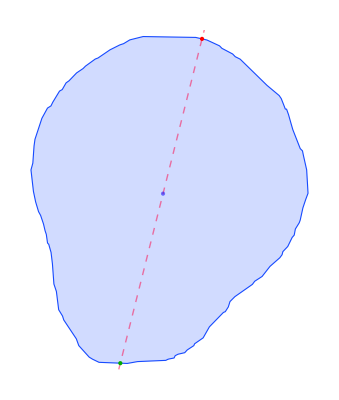
{-Graphics-,{717.728,657.164},{749.54,783.143},{682.891,519.206}}

```mathematica
{temp,centroid,pts1,pts2}=bisectMask[m1,True]
```

```mathematica
(* boundary pts *)
```

```mathematica
perimeterpts=PixelValuePositions[MorphologicalPerimeter@m1,1];
```

```mathematica
(* normalized principle direction *)
```

```mathematica
norm=Normalize[Subtract[pts2,pts1]];
```

```mathematica
First@pts2 ≠ First@pts1
```

True

```mathematica
(* rotation angle *)
```

```mathematica
θ=VectorAngle[norm,{0,1}](180/π);
grad=(pts2[[2]]-pts1[[2]])/(pts2[[1]]-pts1[[1]]);
```

```mathematica
θ=Which[grad>0,If[θ>90,-θ,θ],
grad<0,If[θ<90,-θ,θ]
];
```

```mathematica
(* rotation matrix to rotate perimeter *)
```

```mathematica
rotateFun=RotationTransform[θ Degree,norm]
```

TransformationFunction[(-0.969565 | 0.244833 | -0.244833
-0.244833 | -0.969565 | -1.96957
0. | 0. | 1.)]

```mathematica
(* rotated image *)
```

```mathematica
dim={1024,1024};
```

```mathematica
canvas=ConstantImage[0,dim];
rotatedpts=rotateFun[perimeterpts~Append~centroid];
translationFn = TranslationTransform[dim/2-Last@rotatedpts];
transpts= Abs[translationFn@Most@rotatedpts];
rotatedImg=ReplacePixelValue[canvas,transpts-> 1]//FillingTransform;
```

```mathematica
{Total[rotatedImg],originalArea}
```

{44864.,44879.}

```mathematica
100((Max[#]-Min[#])/Max[#])&@{Total[rotatedImg],originalArea}
```

0.0334232

```mathematica
(* geometric mesh of the rotated image *)
```

```mathematica
imgrotatedMesh=ImageMesh[rotatedImg]
```

-Graphics-

```mathematica
Abs[(Area[imgrotatedMesh]-originalArea)/originalArea]*100
```

0.0327259

```mathematica
(* 
orderedpts=rotatedpts[[ Last@FindShortestTour[rotatedpts]]];
meshorderedpts=MeshRegion[orderedpts,Polygon@Range[Length@orderedpts]];
Abs[(Area[meshorderedpts]-originalArea)/originalArea]*100
*)
```

```mathematica
(* rotating 2D mesh pts about the y axis *)
```

```mathematica
centroidMesh= Append[RegionCentroid[imgrotatedMesh],0];
mesh2Dpts=MeshPrimitives[imgrotatedMesh,0]/.Point[x_]:> x;
rotateTransform=RotationTransform[3Degree,{0,1,0},centroidMesh];
mesh3Dpts=NestList[rotateTransform,ArrayFlatten[{{mesh2Dpts,0}}],59];
```

```mathematica
Graphics3D[{XYZColor[0,0,1,0.2],Point/@mesh3Dpts},Boxed->False]
```

-Graphics3D-

```mathematica
(* convex hull volume *)
```

```mathematica
hullmesh=ConvexHullMesh[Flatten[mesh3Dpts,1]]
```

-Graphics3D-

```mathematica
Values@(First@@Solve[4/3Pi r^3 ==Volume[hullmesh],r∈Reals])
```

116.262